```mathematica
ClearAll["Global`*"];
```

```mathematica
coords = {t,r,θ,ϕ};
n=Length[coords];
rplus = M+Sqrt[M^2-a^2];
tt=2 M r/ρ-1;
rr=ρ/Δ;
θθ=ρ;
ϕϕ=(Δ+(2 M r (r^2+a^2))/ρ)Sin[θ]^2;
tϕ=+2a M r Sin[θ]^2/ρ; 
metric={{tt,0,0,tϕ},{0,rr,0,0},{0,0,θθ,0},{tϕ,0,0,ϕϕ}};
metric//MatrixForm;
inversemetric=Simplify[Inverse[metric]];
inversemetric //MatrixForm;
```

```mathematica
(*M=0.415392;a=0.414068;
tt/.r->12/.θ->π/2
rr/.r->12/.θ->π/2
θθ/.r->12/.θ->π/2
ϕϕ/.r->12/.θ->π/2
tϕ/.r->12/.θ->π/2*)
```

```mathematica
a=.;M=.;
ρ=r^2+a^2 Cos[θ]^2;
Δ=r^2 - 2 M r+ a^2;
christoffel:=christoffel=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*
(D[metric[[s,j]],coords[[k]] ]+
D[metric[[s,k]],coords[[j]] ]-D[metric[[j,k]],coords[[s]] ]),{s,1,n}],
{i,1,n},{j,1,n},{k,1,n}] ]
listchristoffel:=Table[If[UnsameQ[christoffel[[i,j,k]],0],{ToString[Γ[i,j,k]],christoffel[[i,j,k]]}] ,{i,1,n},{j,1,n},{k,1,j}]
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]]coords[[j]]' coords[[k]]',{j,1,n},
{k,1,n}],{i,1,n}]]
listgeodesic:=Table[{"d/dτ"ToString[coords[[i]]'],"=",geodesic[[i]]},{i,1,n}]
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]]coords[[j]]' coords[[k]]',{j,1,n},
{k,1,n}],{i,1,n}]]
```

```mathematica
computeSoln[maxτi_,ivsi_,icsi_]:=Block[{ivs,ics,i,χ,tmp,soln},
ics=icsi;
ivs=Join[{χ},ivsi];
tmp=metric;
tmp=tmp/.Table[coords[[i]]->ics[[i]],{i,0,n}];
tmp=ivs.(tmp.ivs);
τend = maxτi;
χslv=Solve[tmp==uinvar,χ];
ivs[[1]]=Last[χ/.χslv];
deq=Table[coords[[i]]''[τ]==(geodesic[[i]]/.Join[Table[coords[[i]]'->coords[[i]]'[τ],{i,1,n}],Table[coords[[i]]->coords[[i]][τ],{i,1,n}]]),{i,1,n}];
deq=Join[deq,Table[coords[[i]]'[0]==ivs[[i]],{i,1,n}],Table[coords[[i]][0]==ics[[i]],{i,1,n}]];
soln=NDSolve[deq,coords,
{τ,0,maxτi},
Method->{"EventLocator","Event":>(r[τ]≤1.05*rplus),"EventAction":>Throw[τend=τ,"StopIntegration"]}
];
soln]
(* this next function translates from spherical coordinates to Cartesian coordinates to make plotting simpler *)
sphslnToCartsln[soln_]:=Block[{xs,ys,zs},xs=r[τ] Sin[θ[τ]] Cos[ϕ[τ]]/.soln ;ys=r[τ] Sin[θ[τ]] Sin[ϕ[τ]]/.soln;zs=r[τ] Cos[θ[τ]]/.soln;{xs,ys,zs}]
(* This one calculates u dot u *)
udotu[solni_,τval_]:=Block[{xα,uα},xα=Table[coords[[i]][τ]/.solni,{i,1,n}]//Flatten; uα=D[xα,τ];
xα=xα/.τ->τval;uα=uα/.τ->τval;uα.((metric/.Table[coords[[i]]->xα[[i]],{i,1,n}]).uα)]
(* And this one prints out the coordinates *)
coordlist[τin_]:=Table[ToString[coords[[i]]]<>" = "<>{ToString[coords[[i]][τin]/.soln//First]},{i,1,n}]
```

```mathematica
(* Define various plotting functions *)
genXYPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
xyz=sphslnToCartsln[computeSoln[mτ,ivsin,icsin]];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
ParametricPlot[Evaluate[{xyz[[1]],xyz[[2]]}//Flatten],{τ,0,τend},AxesLabel->{x,y},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genXZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
xyz=sphslnToCartsln[computeSoln[mτ,ivsin,icsin]];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
ParametricPlot[Evaluate[{xyz[[1]],xyz[[3]]}//Flatten],{τ,0,τend},AxesLabel->{x,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genYZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
xyz=sphslnToCartsln[computeSoln[mτ,ivsin,icsin]];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
ParametricPlot[Evaluate[{xyz[[2]],xyz[[3]]}//Flatten],{τ,0,τend},AxesLabel->{y,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genXYZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
xyz=sphslnToCartsln[computeSoln[mτ,ivsin,icsin]];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
ParametricPlot3D[Evaluate[Re[xyz]//Flatten],{τ,0,τend},AxesLabel->{x,y,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
```

```mathematica
hitOrMiss[mτ_,icsin_,ivsin_]:=Block[{xyz},
xyz=sphslnToCartsln[computeSoln[mτ,ivsin,icsin]];
If[mτ==τend,0,1]]
```

```mathematica
bisectionEdge[mτ_,icsin_,dθin_,dϕ1_,dϕ2_,eps_] := Block[{dϕOne,dϕTwo,k},
dϕOne=dϕ1;
dϕTwo=dϕ2;
k=0;
While[Abs[dϕTwo-dϕOne]/2> eps,
resultOne = hitOrMiss[mτ,icsin,{dr,dθin,dϕOne}];
resultTwo = hitOrMiss[mτ,icsin,{dr,dθin,(dϕTwo+dϕOne)/2}];
If[resultOne == resultTwo,dϕOne=(dϕTwo+dϕOne)/2,dϕTwo=(dϕTwo+dϕOne)/2];
k=k+1];
{k,(dϕOne+dϕTwo)/2}
]
```

```mathematica
edgeFinder[mτ_,icsin_,dθin_,dϕ1_,dϕ2_,num_,eps_] := Block[{shots,stepdϕ,firstEdge,secondEdge},
stepdϕ = Abs[dϕ1-dϕ2]/num;
shots = Table[{i,hitOrMiss[τValue,icsin,{dr,dθin,i}]},{i,dϕ1,dϕ2,stepdϕ}];
m = 0;
If[Sum[shots[[i,2]],{i,1,Length[shots]}]>0,
Do[
If[shots[[i,2]] - shots[[i-1,2]]==1,firstEdge = {shots[[i-1,1]],shots[[i,1]]}];
If[shots[[i,2]] - shots[[i-1,2]]==-1,secondEdge = {shots[[i-1,1]],shots[[i,1]]}]
,{i,2,Length[shots]}];
leftEdge = bisectionEdge[mτ,icsin,dθin,firstEdge[[1]],firstEdge[[2]],eps];
rightEdge =bisectionEdge[mτ,icsin,dθin,secondEdge[[1]],secondEdge[[2]],eps];
{leftEdge,rightEdge},{{0,Null},{0,Null}}]
]
```

```mathematica
findShadow[mτ_,icsin_,initial_,max_,dθmax_,const_,eps_,compact_] := Block[{leftEdge,rightEdge,edges},
points = {};
Do[
If[compact==1,
dθ = If[i==max,dθmax,N[i/(i+const)*dθmax]],
dθ = If[i==max,dθmax,N[(1-(max-i)/(max-initial))*dθmax]]];
edges = edgeFinder[mτ,icsin,dθ,dϕ1,dϕ2,num,eps];
leftEdge = edges[[1,2]];
rightEdge = edges[[2,2]];
(*num=If[Mod[i,3]==0,num=num+1,num];*)
If[leftEdge =!= Null && rightEdge =!= Null,
dϕ1 = leftEdge;
dϕ2 = rightEdge;
AppendTo[points,{dϕ1,dθ}];
AppendTo[points,{dϕ2,dθ}];
, Break[]
];
,{i,initial,max}];
{points}
]
```

```mathematica
τend=.;uinvar = 0;
M=0.415392;a=0.414068;rplus=M+Sqrt[M^2-a^2];
ics = {0,12,π/2,π/4};
num=20; (* from 10 to 20 didn't increase computation time much *)
eps = 10*^-10;
τValue = 500;
dr=-0.15;
dϕ1=-0.05; (* increasing here makes trouble if the number of points, in num, don't manage to hit the width of the shadow *)
dϕ2=0.05;
```

```mathematica
initial1=0;max1 = 10; dθmax1 = 0.0015;
shadow1 =AbsoluteTiming[findShadow[τValue,ics,initial1,max1,dθmax1,1,eps,0]];
```

30.03966

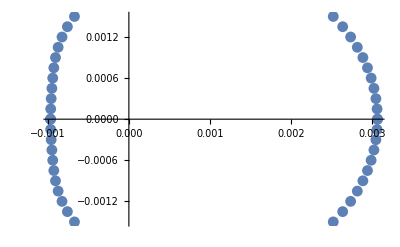

```mathematica
topShadow1 = shadow1[[2]];
time1 = shadow1[[1]]
bottomShadow1 = Table[{topShadow1[[1,i,1]],-topShadow1[[1,i,2]]},{i,1,Length[topShadow1[[1]]]}];
completeShadow1 = Join[topShadow1[[1]],bottomShadow1];
ListPlot[completeShadow1]
```

```mathematica
topShadow1
```

{{{-0.000967928,0.},{0.00307184,0.},{-0.00096586,0.00015},{0.00306704,0.00015},{-0.000960043,0.0003},{0.00305255,0.0003},{-0.000951357,0.00045},{0.0030282,0.00045},{-0.000940716,0.0006},{0.00299366,0.0006},{-0.000927371,0.00075},{0.00294843,0.00075},{-0.00090663,0.0009},{0.00289182,0.0009},{-0.000874095,0.00105},{0.00282286,0.00105},{-0.00082596,0.0012},{0.00274022,0.0012},{-0.000759594,0.00135},{0.00264205,0.00135},{-0.00067235,0.0015},{0.00252566,0.0015}}}

```mathematica
dϕ1=topShadow1[[1,Length[topShadow1[[1]]]-1,1]]
dϕ2=topShadow1[[1,Length[topShadow1[[1]]],1]]
const = 1;
initial2=0;
While[initial2/(initial2+1)*dθmax2≤dθmax1,
initial2+=1;
]
max2 = 50; dθmax2 = 0.0023;
shadow2 =AbsoluteTiming[findShadow[τValue,ics,initial2,max2,dθmax2,const,eps,1]];
```

-0.00067235

0.00252566

110.96792

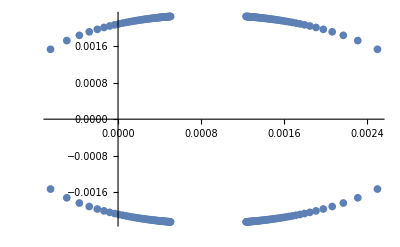

```mathematica
topShadow2 = shadow2[[2]];
time2 = shadow2[[1]]
bottomShadow2 = Table[{topShadow2[[1,i,1]],-topShadow2[[1,i,2]]},{i,1,Length[topShadow2[[1]]]}];
completeShadow2 = Join[topShadow2[[1]],bottomShadow2];
ListPlot[completeShadow2]
```

2.350126

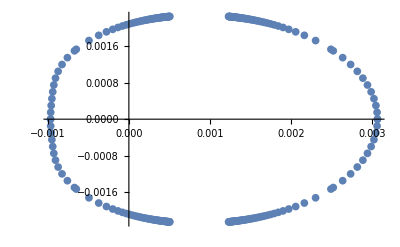

```mathematica
(time1+time2)/60
ListPlot[Join[completeShadow1,completeShadow2]]
```

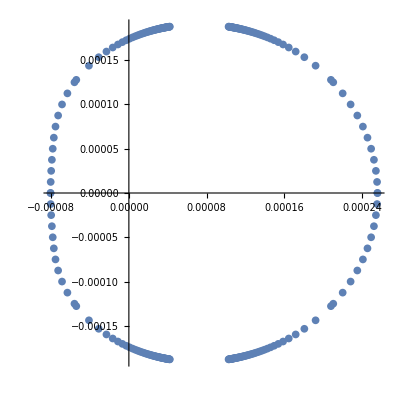

```mathematica
shadow = Join[completeShadow1,completeShadow2];
obsShadow  = Table[0,{i,1,Length[shadow]}];
Do[
xObs=shadow[[i,1]]/Sqrt[ϕϕ/.r->ics[[2]]/.θ->ics[[3]]];
yObs=shadow[[i,2]]/Sqrt[θθ/.r->ics[[2]]/.θ->ics[[3]]];
zObs=-dr/Sqrt[rr/.r->ics[[2]]/.θ->ics[[3]]];
α=ArcTan[Sqrt[xObs^2+yObs^2]/zObs];
β=ArcTan[yObs/xObs];
obsShadow[[i]] = {xObs,yObs};
,{i,1,Length[shadow]}]
ListPlot[obsShadow,AspectRatio->1]
```